# Project 1: Prolate Spinning Body

Mauricio Coen

AERO 628 Spring 2016

## Angular Velocity Solution

The body has the following inertia matrix:

I=(It | 0 | 0
0 | It | 0
0 | 0 | Ia)

And has a torque applied u, where:

u/It=0.2

Using Euler’s Eqs. of Motion: Since it is an axissymmetric-prolate body, the angular acceleration in the body-3 direction is zero.

l_3=Ia OverDot[ω_3]=0

So we can call ω_3=n which is a constant. Now simplifying the other expressions of Euler Eqs. of Motion:

l_2=n ω_1 (It-Ia)+It OverDot[ω_2]=0

OverDot[ω_2]=(Ia-It)/It n ω_1

u=n ω_2 (Ia-It)+It OverDot[ω_1]

OverDot[ω_1]=u/It+(It-Ia)/It n ω_2

Now, we define the following expressions:

u/It≡l

λ≡(It-Ia)/It n

Which will simplify the angular velocity equations:

OverDot[ω_1]=λ ω_2+l

OverDot[ω_2]=-λ ω_1

Using Euler’s Eqs. of Motion: Since it is an axissymmetric-prolate body, the angular acceleration in the body-3 direction is zero.

l_3=Ia OverDot[ω_3]=0

Differentiating the above and substituting:

ω_2^(..)=-λ OverDot[ω_1]

ω_2^(..)+λ^2 ω_2=λl

The differential equation can be solved by merging the homogeneous solution:

w_(2 H)=a sin (λ t)+b cos (λ t)

With the particular solution ω_(2P)=c:

c= -l/λ

So the general solution is:

ω_2=a sin (λ t)+b cos (λ t)-l/λ

Now we can differentiate when t=0 and plug into the OverDot[ω_2] equation:

OverDot[ω_2]=a cos (λ t(0))-b sin (λ t(0))=-λ ω_1(0)

a=-λ ω_1(0)

ω_2(0)=b cos (λ t(0))-l/λ+(-λ) ω_1(0) sin (λ t(0))

b=l/λ+ω_2(0)

Finally the complete solutions are:

ω_1= ω_1(0) cos (λ t)+(l/λ+ω_2(0)) sin (λ t)

ω_2= ω_1(0) sin (λ t)+(l/λ+ω_2(0)) cos (λ t)-l/λ

## Orientation Angles Solution

Using a 1-2-3 (α , β, γ) rotation sequence, we get the following attitude kinematics matrix:

(α̇
β̇
γ̇)=1/Cos[β] (Cos[γ]
Cos[β] Sin[γ]
-Sin[β]  Cos[γ]-Sin[γ] | 0
Cos[γ] Cos[β]
Sin[γ] Sin[β] | 0
Cos[β])(ω_1
ω_2
ω_3)

Notice that γ̇ can be simplified in the following way:

γ̇=n-tan(β) (ω_1 cos(γ)-ω_2 sin(γ))

Substituting for α̇ in the equation above:.

γ̇=n-α̇ sin(β)

Since we have a prolate body, we can approximate the orientation angles solution with small angle approximations, where Cos[β] ≈ 1 and Sin[β] ≈ β:

α̇=ω_1 cos(γ)-ω_2 sin(γ)

β̇=ω_1 sin(γ)+ω_2 cos(γ)

Now we integrate with respect to time to find closed form solutions of the orientation angles:

∫γ̇ ⅆt = γ = n t

∫[ω_1 cos(γ)-ω_2 sin(γ)]ⅆt= α = (It l (Ia Cos[n t]-It Cos[(Ia n t)/It]))/(Ia (Ia-It) n^2)

∫[ω_1 sin(γ)+ω_2 cos(γ)]ⅆt = β = (It l (Ia Sin[n t]-It Sin[(Ia n t)/It]))/(Ia (Ia-It) n^2)

## Numerical Integration

The full nonlinear system is numerically integrated with Matlab ODE45() to provide a high accuracy solution of the prolate body’s rotation.

## Results

The α and β angles as a function or time are shown in Figure 1. The parameters used are: γ=5 rad/s, It=1, Ia=0.05, initial conditions: all zero except γ.

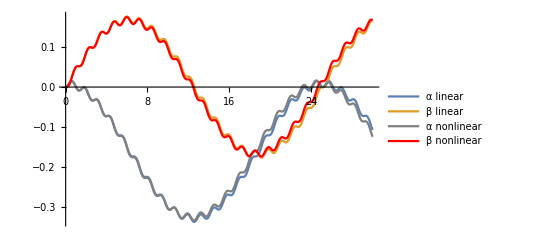

Figure FigureCaption.   Orientation angles over  frequency

As it can be seen. The linear solution tracks the nonlinear solution very well. `

## Fourier Analysis

The linear nutational frequency (F_n) equals ω_3(0), F_n=0.796 Hz.

The linear precessional frequency (F_p) = Ia/It F_n=0.0398 Hz

The nonlinear solution can be transformed with a Fast Fourier Transform and then the frequency spectrum plotted. Below, the frequency spectrum

-Graphics-

Figure FigureCaption.   Orientation angles over  frequency

As it can be seen. The spikes in the frequency domain graph align neatly with the calculated frequencies in the closed form solutions.  This can mean that for the ω_3(0)=5, the linearized analysis correlates with high accuracy to the nonlinear solution.

## Varying the Spin Rate

We can investigate the linear solution’s fidelity by varying the initial ω_3. The slider below can be used to see the change in the time histories of the orientation angles as ω_3 changes.

```mathematica
Manipulate[Plot[{Legended[alphaPlot=(4.21052631578947 Cos[0.050000000000000044 n t]-0.21052631578947367 Cos[n t])/n^2-(4.21052631578947-0.21052631578947367)/n^2,"α"],Legended[betaPlot=(0.21052631578947367 ((19.999999999999982 Sin[0.050000000000000044 n t])/n-Sin[n t]/n))/n,"β"]},{t,0,30},PlotRange->{{0,30},{-2.5,1.5}},Axes->False],{n,0.5,5}]
```

-Graphics-

Figure FigureCaption.   Overlay of both nonlinear and linear solutions. ω_3=4

-Graphics-

Figure FigureCaption.   Overlay of both nonlinear and linear solutions. ω_3=3

-Graphics-

Figure FigureCaption.   Overlay of both nonlinear and linear solutions. ω_3=2

-Graphics-

Figure FigureCaption.   Overlay of both nonlinear and linear solutions. ω_3=1

As it can be seen, the linear solution starts losing the periodic oscillation at ω_3=3, when it reaches 2 rad/s. the linear solution’s slow period is twice that of the nonlinear solution. When it reaches 1 rad/s, the linear solution is completely erroneous and loses track of all information within 5 seconds.